# Hybrid binding energy (0PA)

SF+PN hybrid binding energy after Honet+2025 Sec. III C, eq. (47), truncated at 0PA: the 1PA self-force term ν^2 M E^SF_(1) (eq. 49, from the 1SF redshift) and its PN overlap ν^2 M x Σ E^(SF|PN)_(1) are left out. Divided by ν M:  Ê_H(x, ν, χ) = Ê_geo(x, χ) + Ê_PN(x, ν, χ) - Ê_PN(x, 0, χ),  the same composite as HybridInfFluxNewtNorm in Fluxes/HybridEnFluxes.nb. Units G = c = M = 1, x = (M Ω)^(2/3). The M vs m1 and evolving vs initial spin distinctions (δM, δχ terms of eq. 49) are 1PA and are ignored.

```mathematica
Clear["Global`*"]
```

## SF data: geodesic binding energy

EhatGeo[x, χ] = E_geo/(ν M), eq. (48), closed form from BindingEnergy.wl (also loads Fluxes/FluxInterpolation.wl for rISCO). xISCO[χ] = (rISCO^(3/2) + χ)^(-2/3).

```mathematica
Get["/home/luca/repos/hyb_env_model/Mathematica/BindingEnergy/BindingEnergy.wl"];
```

```mathematica
EhatGeo[x, χ]
```

-1+(1-2 x (1-x^(3/2) χ)^(1/3))/(√((1-x^(3/2) χ) (1+x^(3/2) χ-3 x (1-x^(3/2) χ)^(1/3))))

```mathematica
{xISCO[0.5], xISCO[0.], xISCO[-0.5]}
```

{0.227609,0.166667,0.134538}

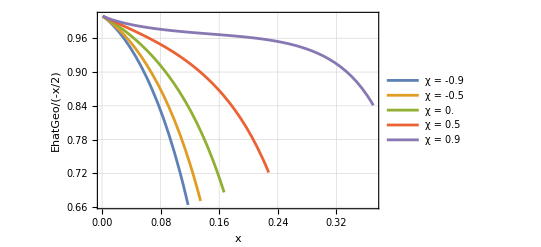

```mathematica
chis = {-0.9, -0.5, 0., 0.5, 0.9};
Plot[Evaluate[Table[ConditionalExpression[EhatGeo[x, a]/(-x/2), x <= xISCO[a]], {a, chis}]], {x, 0.001, xISCO[0.9]}, PlotRange -> All, Frame -> True, GridLines -> Automatic, FrameLabel -> {"x", "EhatGeo/(-x/2)"}, PlotLegends -> (Row[{"χ = ", #}] & /@ chis)]
```

## PN data: binding energy

Source: PNpedia (commit a64de8b), Circular orbits/Spinning/Nonprecessing/Without tidal effects/Constants of motion/Energy/energy_conservative.txt, black holes (κ = λ = 1). Nonspinning and SO/SS 4PN from arXiv:1401.4548, 1711.00283, 2201.05138; SSS 3.5PN from arXiv:1411.4118; quartic-in-spin terms vanish at 4PN.

Conservative (mechanical) energy, not PNpedia's energy_binding.txt: Honet replaces the Bondi mass with the mechanical energy and leaves out the 4PN Schott term (Sec. III C). The binding version adds the b0-dependent Schott term, which only cancels against a matching flux; the Blanchet+2023 4PN flux of HybridEnFluxes.nb has no b0 and pairs with the conservative energy. The Checks chapter verifies binding = conservative + Schott.

Coefficients are relative to the Newtonian -ν M x/2. Spin variables as in PNpedia: s = S/M^2 = (m1^2 χ1 + m2^2 χ2)/M^2, sg = Σ/M^2 = (m2 χ2 - m1 χ1)/M, dl = Δ = (m1 - m2)/M.

## Nonspinning 4PN

The 4.5PN terms vanish for circular orbits. lx = Log[x].

```mathematica
E0[nu_, lx_] := 1;
E1[nu_, lx_] := -3/4 - nu/12;
E2[nu_, lx_] := -27/8 + (19*nu)/8 - nu^2/24;
E3[nu_, lx_] := -675/64 - (155*nu^2)/96 - (35*nu^3)/5184 - (5*nu*(-6889 + 246*Pi^2))/576;
E4[nu_, lx_] := -3969/128 + (301*nu^3)/1728 + (77*nu^4)/31104 + (7*nu^2*(-71207 + 2706*Pi^2))/3456 + nu*(-123671/5760 + (896*EulerGamma)/15 + (448*lx)/15 + (9037*Pi^2)/1536 + (1792*Log[2])/15);
EOrb[nu_, x_] := -(nu*x/2)*(E0[nu, Log[x]] + E1[nu, Log[x]]*x^(1) + E2[nu, Log[x]]*x^(2) + E3[nu, Log[x]]*x^(3) + E4[nu, Log[x]]*x^(4));
```

## Spin-Orbit 4PN

SO terms at x^(3/2), x^(5/2), x^(7/2) relative to Newtonian; the x^4 term vanishes.

```mathematica
ESO15[nu_, s_, sg_, dl_] := (14*s)/3 + 2*dl*sg;
ESO25[nu_, s_, sg_, dl_] := 11*s + 3*dl*sg + (nu*(-61*s - 30*dl*sg))/9;
ESO35[nu_, s_, sg_, dl_] := nu*((-367*s)/4 - 39*dl*sg) + (27*(5*s + dl*sg))/4 + nu^2*((29*s)/12 + (5*dl*sg)/4);
ESO[nu_, x_, s_, sg_, dl_] := -(nu*x/2)*(ESO15[nu, s, sg, dl]*x^(3/2) + ESO25[nu, s, sg, dl]*x^(5/2) + ESO35[nu, s, sg, dl]*x^(7/2));
```

## Spin-Spin 4PN

```mathematica
ESS2[nu_, s_, sg_, dl_] := -4*s^2 - 4*dl*s*sg - sg^2 + 4*nu*sg^2;
ESS3[nu_, s_, sg_, dl_] := (-10*nu^2*sg^2)/3 + (5*nu*(4*s^2 + 4*dl*s*sg - 9*sg^2))/6 + (5*(-10*s^2 + 12*dl*s*sg + 9*sg^2))/18;
ESS4[nu_, s_, sg_, dl_] := (7*nu^3*sg^2)/18 - (7*(88*s^2 + 12*dl*s*sg - 9*sg^2))/24 + (7*nu*(2720*s^2 + 2172*dl*s*sg + 81*sg^2))/216 - (7*nu^2*(4*s^2 + 4*dl*s*sg + 561*sg^2))/72;
ESS[nu_, x_, s_, sg_, dl_] := -(nu*x/2)*(ESS2[nu, s, sg, dl]*x^(2) + ESS3[nu, s, sg, dl]*x^(3) + ESS4[nu, s, sg, dl]*x^(4));
```

## Spin-Spin-Spin 3.5PN

```mathematica
ESSS35[nu_, s_, sg_, dl_] := 8*nu*sg^2*(5*s + dl*sg) - 2*(4*s^3 + 8*dl*s^2*sg + 5*s*sg^2 + dl*sg^3);
ESSS[nu_, x_, s_, sg_, dl_] := -(nu*x/2)*(ESSS35[nu, s, sg, dl]*x^(7/2));
```

## Full PN binding energy

Spin map for a spinning primary (m1, spin χ) and a nonspinning secondary, as in HybridEnFluxes.nb and HybridModes.nb (Honet eq. B6): s = (1 + Δ)^2 χ/4, sg = -(1 + Δ) χ/2, Δ = Sqrt[1 - 4ν]. EhatPN = E_PN/(ν M); EhatPN0 is its ν -> 0 limit, i.e. the PN expansion of EhatGeo (the SF|PN overlap of eq. 47).

```mathematica
EPN[x_, nu_, s_, sg_, dl_] := EOrb[nu, x] + ESO[nu, x, s, sg, dl] + ESS[nu, x, s, sg, dl] + ESSS[nu, x, s, sg, dl];
δOf[ν_] := Sqrt[1 - 4*ν];
sOf[ν_, χ_] := ((1 + δOf[ν])/2)^2*χ;
σOf[ν_, χ_] := -((1 + δOf[ν])/2)*χ;
EhatPN[x_, ν_, χ_] = Collect[Expand[EPN[x, ν, sOf[ν, χ], σOf[ν, χ], δOf[ν]]/ν], x, Simplify];
EhatPN0[x_, χ_] = Collect[Normal[Series[EhatPN[x, ν, χ], {ν, 0, 0}]], x, Simplify]
```

-x/2+(3 x^2)/8-4/3 x^(5/2) χ-4 x^(7/2) χ-27/2 x^(9/2) χ+x^4 (675/128+(65 χ^2)/36)+1/16 x^3 (27+8 χ^2)+7/768 x^5 (1701+1072 χ^2)

## Hybrid binding energy

EhatHyb = E_H/(ν M) (eq. 47 at 0PA); HybridBindingEnergy[x, ν, χ] = ν M EhatHyb with M = 1.

```mathematica
EhatHyb[x_, ν_, χ_] := EhatGeo[x, χ] + EhatPN[x, ν, χ] - EhatPN0[x, χ];
HybridBindingEnergy[x_, ν_, χ_] := ν*EhatHyb[x, ν, χ]
```

Newtonian-normalised energies E/(-ν M x/2) for q = 14 (as in Honet Figs. 9-10), up to the ISCO (gray line).

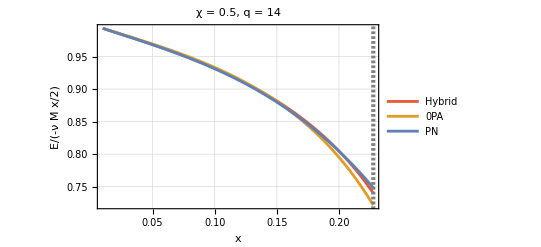
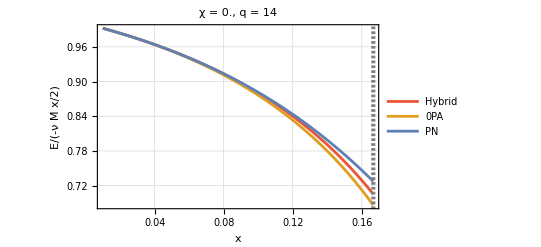
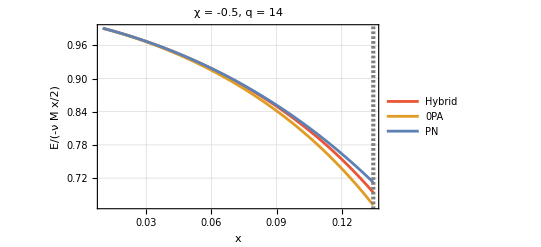

```mathematica
blue = ColorData[97][1];
orange = ColorData[97][2];
red = RGBColor[234/255, 85/255, 54/255];
q = 14;
nuq = q/(1 + q)^2;
newtPlot[a_] := Plot[{EhatHyb[x, nuq, a]/(-x/2), EhatGeo[x, a]/(-x/2), EhatPN[x, nuq, a]/(-x/2)}, {x, 0.01, xISCO[a]}, PlotRange -> All, PlotStyle -> {red, orange, blue}, PlotLegends -> {"Hybrid", "0PA", "PN"}, Frame -> True, GridLines -> Automatic, FrameLabel -> {"x", "E/(-ν M x/2)"}, PlotLabel -> Row[{"χ = ", a, ",  q = ", q}], Epilog -> {GrayLevel[0.5], AbsoluteThickness[3], AbsoluteDashing[{2, 1.5}], InfiniteLine[{xISCO[a], 0}, {0, 1}]}];
newtPlot /@ {0.5, 0., -0.5}
```

## Comparison with Honet Fig. 10

Fig. 10 of Honet+2025: binding energy in units of M for q = 14 (ν = 14/225), χ = 0.5, 0, -0.5, each curve shifted to vanish at the left edge x_i of its panel. The paper gives no x_i; x_i and the right edges were read off a 400 dpi render of the figure by calibrating the axis ticks: x_i = 0.091, 0.091, 0.079 (the last two match the windows of Fig. 11), right edges 0.230, 0.170, 0.140. The figure's ISCO lines fall on xISCO[χ]. Note that the paper's Hybrid (red) includes the 1PA term, which this notebook does not.

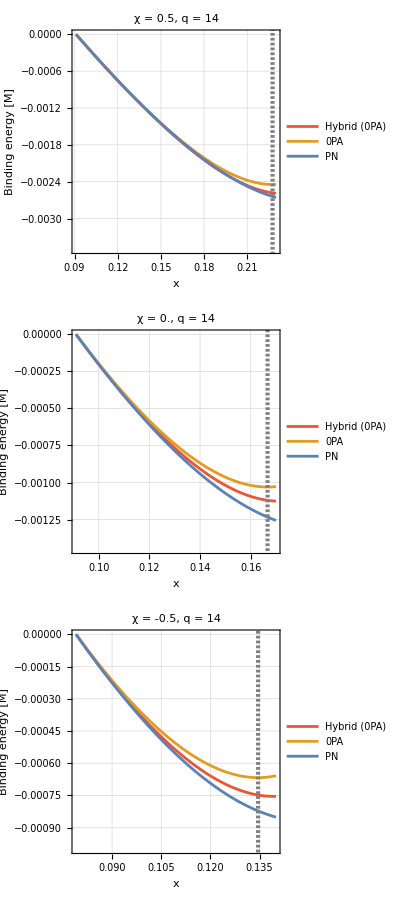

```mathematica
nuF = 14/225.;
fig10 = {{0.5, 0.091, 0.230, {-0.0035, 0.}}, {0., 0.091, 0.170, {-0.00145, 0.}}, {-0.5, 0.079, 0.140, {-0.001, 0.}}};
Eshift[f_, xi_, x_] := nuF*(f[x] - f[xi]);
models[a_] := {EhatHyb[#, nuF, a] &, EhatGeo[#, a] &, EhatPN[#, nuF, a] &};
fig10Panel[{a_, xi_, xf_, yr_}] := Plot[Evaluate[Eshift[#, xi, x] & /@ models[a]], {x, xi, xf}, PlotRange -> {{xi, xf}, yr}, PlotStyle -> {red, orange, blue}, PlotLegends -> Placed[{"Hybrid (0PA)", "0PA", "PN"}, {0.25, 0.3}], Frame -> True, GridLines -> Automatic, FrameLabel -> {"x", "Binding energy [M]"}, PlotLabel -> Row[{"χ = ", a, ",  q = 14"}], Epilog -> {GrayLevel[0.5], AbsoluteThickness[3], AbsoluteDashing[{2, 1.5}], InfiniteLine[{xISCO[a], 0}, {0, 1}]}, ImageSize -> 400];
fig10Plot = Column[fig10Panel /@ fig10]
```

Reference values read off Fig. 10 (reading precision about 1 pixel, 3x10^-6 M): 0PA at the ISCO, PN and Hybrid at the right edge. Last column: ours/Fig.10 - 1.

```mathematica
fig10Ref = {{0.5, "0PA", "ISCO", -0.002442}, {0.5, "PN", 0.230, -0.002655}, {0.5, "Hybrid", 0.230, -0.002619}, {0., "0PA", "ISCO", -0.001029}, {0., "PN", 0.170, -0.001255}, {0., "Hybrid", 0.170, -0.001179}, {-0.5, "0PA", "ISCO", -0.000668}, {-0.5, "PN", 0.140, -0.000851}, {-0.5, "Hybrid", 0.140, -0.000814}};
fig10Ours[{a_, mod_, xp_, ref_}] := Module[{xi = SelectFirst[fig10, First[#] == a &][[2]], xv = If[xp === "ISCO", xISCO[a], xp], f, e}, f = Switch[mod, "Hybrid", EhatHyb[#, nuF, a] &, "0PA", EhatGeo[#, a] &, "PN", EhatPN[#, nuF, a] &]; e = Eshift[f, xi, xv]; {a, mod, xv, ref, e, e/ref - 1}];
TableForm[fig10Ours /@ fig10Ref, TableHeadings -> {None, {"χ", "model", "x", "Fig. 10", "ours", "ours/Fig.10 - 1"}}]
```

χ | model | x | Fig. 10 | ours | ours/Fig.10 - 1
0.5 | 0PA | 0.227609 | -0.002442 | -0.00244637 | 0.001791
0.5 | PN | 0.23 | -0.002655 | -0.00265782 | 0.00106329
0.5 | Hybrid | 0.23 | -0.002619 | -0.00258916 | -0.0113919
0. | 0PA | 0.166667 | -0.001029 | -0.00103045 | 0.00141376
0. | PN | 0.17 | -0.001255 | -0.0012558 | 0.000639252
0. | Hybrid | 0.17 | -0.001179 | -0.00112584 | -0.0450888
-0.5 | 0PA | 0.134538 | -0.000668 | -0.000666998 | -0.0014994
-0.5 | PN | 0.14 | -0.000851 | -0.000850854 | -0.000171346
-0.5 | Hybrid | 0.14 | -0.000814 | -0.000753999 | -0.0737109

Quality of the comparison. 0PA and PN reproduce the paper's orange and blue curves to within 0.2% (|ours/Fig.10 - 1| = 0.18%, 0.14%, 0.15% for 0PA and 0.11%, 0.06%, 0.02% for PN at χ = 0.5, 0, -0.5), i.e. at the reading precision of the figure (about 1 pixel). This validates eq. (48), the conservative PN energy, the spin map, ν = 14/225 and the shift convention.

The 0PA hybrid does not reproduce the paper's red curve near the ISCO: at the right edge it is 1.1% (χ = 0.5), 4.5% (χ = 0) and 7.4% (χ = -0.5) less bound than the paper's Hybrid, and lies between the 0PA and PN curves. The difference is the missing 1PA term ν^2 M (E^SF_(1) - E^(SF|PN)_(1)), the 1SF energy beyond 4PN. In the paper this term partly cancels the 0PA beyond-4PN remainder ν M (EhatGeo - EhatPN0), so their Hybrid sits close to PN and NR; without it the 0PA hybrid is farther from NR than PN near the ISCO. The binding energy needs the 1PA redshift term before it is used in the waveform model.

## Checks

## PN sectors vs PNpedia

Expect {0, 0, 0}: (1) the four sectors sum back to the spinning conservative file; (2) the nonspinning sector equals the nonspinning conservative file; (3) binding = conservative + Schott in the PNpedia files.

```mathematica
pnDir = "/home/luca/repos/PNpedia/Core post-Newtonian quantities/Circular orbits";
readPN[f_] := ToExpression[Import[FileNameJoin[{pnDir, f}], "Text"]] /. {c -> 1, G -> 1, m -> 1};
eDir = "Spinning/Nonprecessing/Without tidal effects/Constants of motion/Energy/";
eCons = readPN[eDir <> "energy_conservative.txt"];
eBind = readPN[eDir <> "energy_binding.txt"];
eSchott = readPN[eDir <> "energy_Schott.txt"];
eConsNS = readPN["Nonspinning/Without tidal effects/Constants of motion/Energy/energy_conservative.txt"];
{Simplify[EPN[x, ν, s, σ, δ] - eCons], Simplify[EOrb[ν, x] - eConsNS, x > 0], Simplify[eBind - eCons - eSchott]}
```

{0,0,0}

## Test-mass limit

EhatPN0 must equal the x-expansion of EhatGeo through x^5 (4PN): expect 0. The first missing terms are x^(11/2) (spin-orbit) and x^6.

```mathematica
Simplify[Normal[Series[EhatGeo[x, χ], {x, 0, 5}]] - EhatPN0[x, χ]]
```

0

```mathematica
nextGeo = Simplify[Normal[Series[EhatGeo[x, χ], {x, 0, 6}]] - Normal[Series[EhatGeo[x, χ], {x, 0, 5}]]]
```

-5/81 x^(11/2) χ (729+40 χ^2)+(3 x^6 (15309+14688 χ^2+128 χ^4))/1024

Residual (EhatGeo - EhatPN0)/nextGeo: tends to 1 as x -> 0.

```mathematica
TableForm[Table[(EhatGeo[x0, a] - EhatPN0[x0, a])/(nextGeo /. {x -> x0, χ -> a}), {x0, {0.02, 0.04, 0.06, 0.1}}, {a, {-0.5, 0., 0.5}}], TableHeadings -> {{0.02, 0.04, 0.06, 0.1}, {"χ = -0.5", "χ = 0", "χ = 0.5"}}]
```

| χ = -0.5 | χ = 0 | χ = 0.5
0.02 | 1.07003 | 1.06114 | 1.07389
0.04 | 1.14978 | 1.13025 | 1.16408
0.06 | 1.24193 | 1.20899 | 1.27756
0.1 | 1.47801 | 1.40477 | 1.64247